```mathematica
情况一：光源（焦点）在刀片前。刀片后的波前为(仅考虑x方向)：
```

```mathematica
T1[x_]:=Exp[I x^2]
```

```mathematica
其夫琅禾费衍射场为
```

```mathematica
Integrate[Exp[-I k x]*T1[x],{x,0,∞},Assumptions->k∈Reals]
```

(1/2+ⅈ/2) ⅇ^(-(ⅈ k^2)/4) √(π/2) (1+(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])

```mathematica
光强分布为：
```

```mathematica
I1[k_]:=Abs[(1/2+ⅈ/2) ⅇ^(-(ⅈ k^2)/4) √(π/2) (1+(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])]^2
```

```mathematica
作图如下：
```

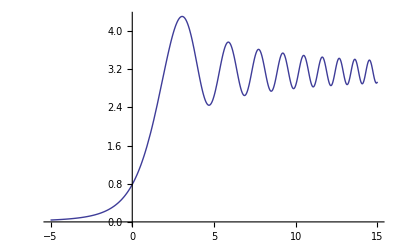

```mathematica
Plot[I1[x],{x,-5,15}]
```

```mathematica
当光源在刀片后的时候，波前为：
```

```mathematica
T2[x_]:=Exp[-I x^2]
```

```mathematica
其夫琅禾费衍射场为
```

```mathematica
Integrate[Exp[-I k x]*T2[x],{x,0,∞},Assumptions->k∈Reals]
```

(1/2+ⅈ/2) ⅇ^((ⅈ k^2)/4) √(π/2) (-ⅈ-(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])

```mathematica
光强：
```

```mathematica
I2[k_]:=Abs[(1/2+ⅈ/2) ⅇ^((ⅈ k^2)/4) √(π/2) (-ⅈ-(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])]^2
```

```mathematica
作图：
```

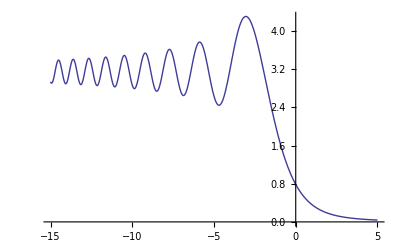

```mathematica
Plot[I2[x],{x,-15,5}]
```

```mathematica
将I2与I1进行比较（为比较方便，将I2向上平移了 0.1）：
```

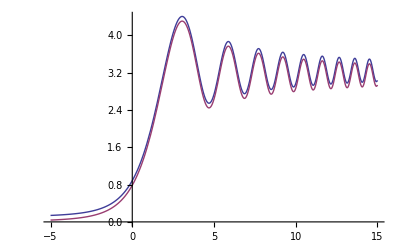

```mathematica
Plot[{I2[-x]+.1,I1[x]},{x,-5,15}]
```

```mathematica
可以看出I1[x]，I2[-x]是一样的
虽然方向不同，但极小值点的间距没有变化。
```